The data we’re looking at:

-Graphics-

Matrix plot of the full feature vectors for a sample of 50 images:

-Graphics-

The neural net used for training the USA dataset:

```mathematica
geoNet=NetChain[ 
{
200,Ramp,DropoutLayer[0.3],
100,Ramp,
20,
1
},
"Input"->{324},(* our feature vectors are 335-dimensional *)
"Output"->NetDecoder["Scalar"] (* decode into a single number: zoom in km *)
];
```

Plot of predicted vs. actual image zoom, evaluated on USA net with feature extraction:

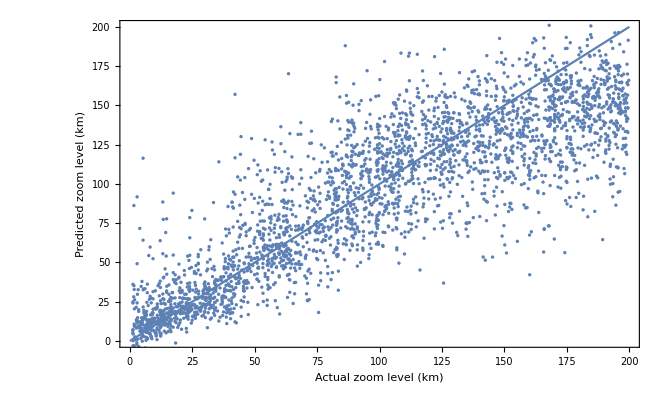

Comparison of Manhattan imagery in DigitalGlobe (left) and Wolfram satellite data (right) :

-Graphics-

Plot of predicted vs. actual image zoom, using Wolfram satellite images, evaluated on USA net with feature extraction :